```mathematica
Clear["Global`*"]
f[x_,y_]=UnitBox[x] UnitBox[y];
g[wx_,wy_]=FourierTransform[f[x,y],{x,y},{wx,wy}];
Plot3D[Evaluate[g[wx,wy]],{wx,-20,20},{wy,-20,20},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[Evaluate[g[wx,wy]],{wx,-20,20},{wy,-20,20},PlotStyle->RGBColor[1.,0.88,0.28],PlotRange->All]
```

-Graphics3D-

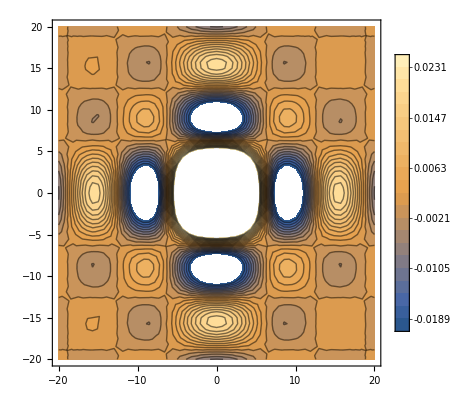

```mathematica
ContourPlot[Evaluate[g[wx,wy]],{wx,-20,20},{wy,-20,20},Contours->30,PlotLegends->Automatic]
```